```mathematica
tb=turboBoundary[1750,250,0.99,246,.97,1.003,0.6,0.9,4.7,26,30,835,1.781]
```

turboBoundary[1750,250,0.99,246,0.97,1.003,0.6,0.9,4.7,26,30,835,1.781]

```mathematica
tc=compressorRequirement[tb]
```

compressorRequirement[turboBoundary[1750,250,0.99,246,0.97,1.003,0.6,0.9,4.7,26,30,835,1.781]]

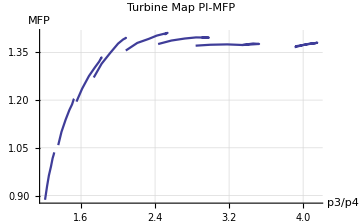

```mathematica
Show[Extract[plotTMaps[mapList[[4]]],{1,1,1}],
ListLinePlot[{{tt["p3p4"],tt["mfp"]}},PlotStyle->{Black,Thick},PlotMarkers->{Automatic, 10}],PlotRange->All]
```

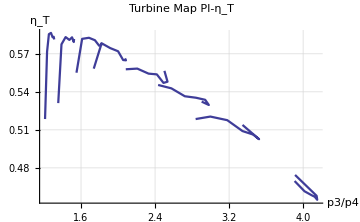

```mathematica
Show[Extract[plotTMaps[mapList[[4]]],{1,1,2}],
ListLinePlot[{{tt["p3p4"],tt["etaT"]}},PlotStyle->{Black,Thick},PlotMarkers->{Automatic, 10}],PlotRange->All]
```

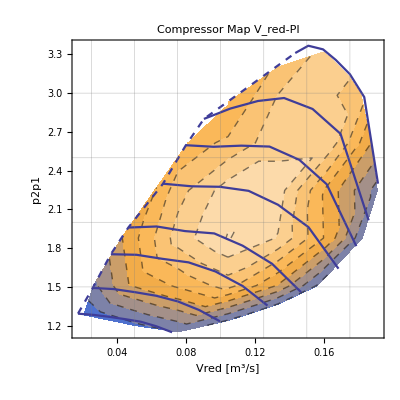

```mathematica
Show[Extract[plotCMaps[mapList[[4]],True],{1,1,1}],ListLinePlot[{{tt["Vred"],tt["p2p1"]}},PlotStyle->{Black,Thick},PlotMarkers->{Automatic, 10}],PlotRange->All]
```

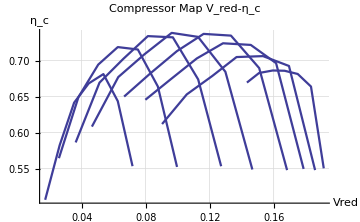

```mathematica
Show[Extract[plotCMaps[mapList[[4]],True],{1,1,2}],ListLinePlot[{{tt["Vred"],tt["etaV"]}},PlotStyle->{Black,Thick},PlotMarkers->{Automatic, 10}],PlotRange->All]
```

```mathematica
(*etacs=readMapEtaV[cr,cmapid];*)
```